# ANALISIS PRACTICA 9

Funciones de varias variables

```mathematica
f[x_, y_, z_]:= x Cos[y] + z Sin [x] + E ^ (x+y+z) + z x^2 + 3 x y
```

```mathematica
Plot3D[f[x, y, z], {x, -3, 3}, {y, -2, 2}, {z, -12, 5}]
```

Plot3D::nonopt: Options expected (instead of {z, -12, 5}) beyond position 3 in Plot3D[f[x, y, z], {x, -3, 3}, {y, -2, 2}, {z, -12, 5}]. An option must be a rule or a list of rules.

Plot3D[f[x,y,z],{x,-3,3},{y,-2,2},{z,-12,5}]

No se pueden dibujar funciones de tres variables

```mathematica
g[x_, y_] := x^2 - y^2
```

```mathematica
Plot3D[g[x, y], {x, -10, 10}, {y, -10,  10}]
```

-Graphics3D-

El comando Which[] sirve para dibujar una cierta parte.

```mathematica
Plot3D[Which[x^2 + y^2 ≤ 5, g[x, y]], {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

La funcion ContourPlot[] dibuja lineas de nivel

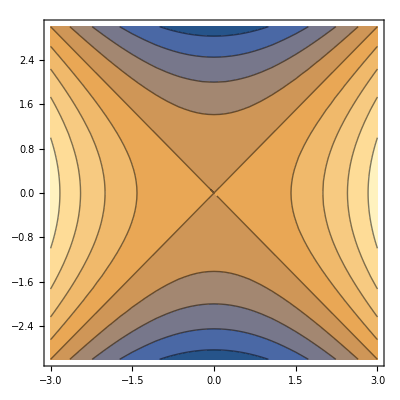

```mathematica
ContourPlot[g[x, y], {x, -3, 3}, {y, -3, 3}]
```

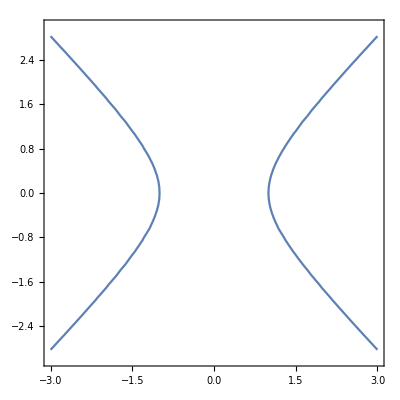

```mathematica
ContourPlot[g[x, y] == 1, {x, -3, 3}, {y, -3, 3}]
```

```mathematica
h [x_, y_] := Abs[x] + Abs[y];
```

```mathematica
k[x_,  y_] := x*y/(x^2 + y^2)
```

```mathematica
Plot3D[k[x,  y], {x, -3, 3}, {y, -3, 3}, PlotPoints->40, Boxed-> False, Axes -> False, Mesh->None]
```

-Graphics3D-

```mathematica
Limit[k[x, y] /. y-> t x, x -> 0]
```

t/(1+t^2)

```mathematica
Limit[k[x, y] /. x -> y^2, y -> 0]
```

0

Derivadas

```mathematica
D[f[x, y, z], {x, 37}, {y, 2}, {z, 3}]
```

ⅇ^(x+y+z)

```mathematica
D[g[x, y], x, y]
```

0

```mathematica
D[f[x, y, z], {x, 1}, {y, 2}] /. {x -> 1, y -> 2, z -> 1}
```

ⅇ^4-Cos[2]

Plano tangente a la grafica de g[x, y] en el punto (1, 2). z = g(1, 2) + Derivada de x (1, 2) (x - 1) + Derivada de y (1, 2) (y - 2);